# Projections

```mathematica
ψ = Sum[c[G]*Exp[ⅈGr],G]/Sqrt[vol];
```

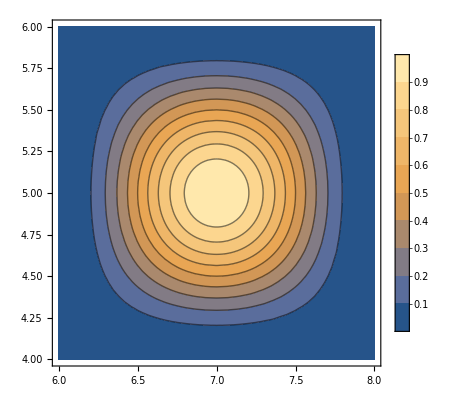

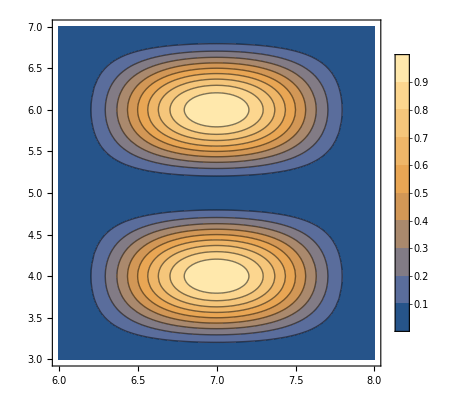

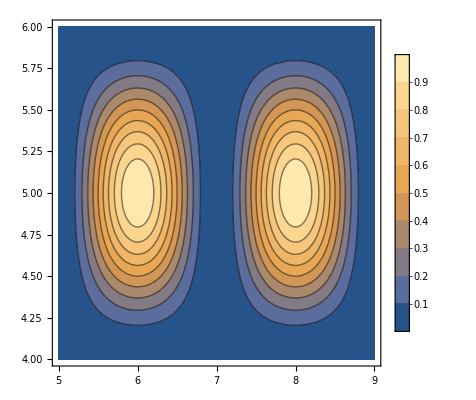

1/(√vol (Gx^2-κ^2) (Gy^2-κ^2))ⅇ^(-ⅈ (Gx (xL+xR)+Gy (yL+yR))) (-ⅈ ⅇ^(ⅈ Gx xR) Gx Cos[(-xc+xL) κ]+ⅈ ⅇ^(ⅈ Gx xL) Gx Cos[(-xc+xR) κ]+ⅇ^(ⅈ Gx xR) κ Sin[(-xc+xL) κ]-ⅇ^(ⅈ Gx xL) κ Sin[(-xc+xR) κ]) (-ⅇ^(ⅈ Gy yR) κ Cos[(yc-yL) κ]+ⅇ^(ⅈ Gy yL) κ Cos[(yc-yR) κ]+ⅈ Gy (ⅇ^(ⅈ Gy yR) Sin[(yc-yL) κ]-ⅇ^(ⅈ Gy yL) Sin[(yc-yR) κ]))

```mathematica
(*Trial Orbitals*)
Clear[L,k];

g1[x_,y_]:=Sin[κ*(x-xc)]*Sin[κ*(y-yc)];
g2[x_,y_]:=Sin[κ*(x-xc)]*Cos[κ*(y-yc)];
g3[x_,y_]:=Cos[κ*(x-xc)]*Sin[κ*(y-yc)];
(*Plane wave basis function (c.c.)*)
basVec[x_,y_,Gx_,Gy_]:= Exp[-ⅈ*(Gx*x+Gy*y)]/Sqrt[vol];

(*Plotting of trial orbitals*)
atCx=7.0;
atCy=5.0;
atR=1.0;
κ=π/(2*atR);
xc=atCx-atR;
yc=atCy-atR;

ContourPlot[g1[x,y]^2,{x,atCx-atR,atCx+atR},{y,atCy-atR,atCy+atR},PlotLegends->Automatic]
ContourPlot[g2[x,y]^2,{x,atCx-atR,atCx+atR},{y,atCy-2*atR,atCy+2*atR},PlotLegends->Automatic]
ContourPlot[g3[x,y]^2,{x,atCx-2*atR,atCx+2*atR},{y,atCy-atR,atCy+atR},PlotLegends->Automatic]

(*Integrals*)
Clear[κ];
Clear[Gx,Gy,xc,yc];
f1[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g1[x,y],{x,xL,xR},{y,yL,yR}];
f2[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g2[x,y],{x,xL,xR},{y,yL,yR}];
f3[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g3[x,y],{x,xL,xR},{y,yL,yR}];

f3[Gx,Gy]
```

## 3 Trial Orbitals per well